## DeleteCell-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 05:20:03
using xCellerator 0.90 and XSSA 1204002

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

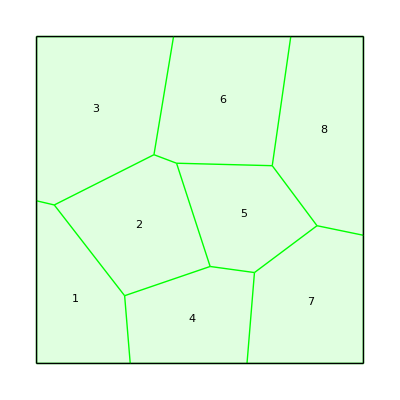

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick]]
```

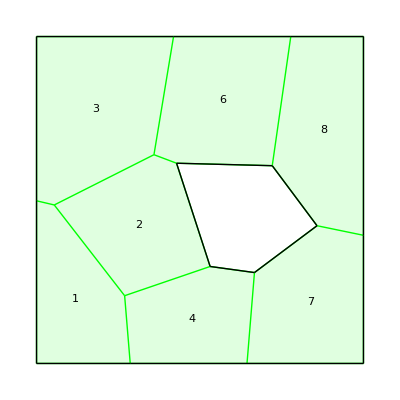

```mathematica
R=DeleteCell[Q,5];
ShowTissue[R, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick]]
```

```mathematica
Q
```

DTissue[{{-44.5763,-1.51875},{-23.0535,-29.2741},{-14.0837,13.8549},{-7.17151,11.2493},{3.10073,-20.3347},{16.6586,-22.1943},{22.0996,10.4946},{35.7909,-7.8663},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-10.7943},{27.7669,50.},{-8.09136,50.},{-50.,-0.24327},{-21.3416,-50.},{14.3774,-50.}},{{1,2},{1,3},{1,16},{2,5},{2,17},{3,4},{3,15},{4,5},{4,7},{5,6},{6,8},{6,18},{7,8},{7,14},{8,13},{9,13},{9,18},{10,13},{10,14},{11,15},{11,16},{12,16},{12,17},{14,15},{17,18}},{1→{23,5,1,3,22},2→{1,4,8,6,2},3→{21,3,2,7,20},4→{25,12,10,4,5},5→{10,11,13,9,8},6→{24,7,6,9,14},7→{15,11,12,17,16},8→{19,14,13,15,18}}]

```mathematica
R
```

DTissue[{{-44.5763,-1.51875},{-23.0535,-29.2741},{-14.0837,13.8549},{-7.17151,11.2493},{3.10073,-20.3347},{16.6586,-22.1943},{22.0996,10.4946},{35.7909,-7.8663},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-10.7943},{27.7669,50.},{-8.09136,50.},{-50.,-0.24327},{-21.3416,-50.},{14.3774,-50.}},{{1,2},{1,3},{1,16},{2,5},{2,17},{3,4},{3,15},{4,5},{4,7},{5,6},{6,8},{6,18},{7,8},{7,14},{8,13},{9,13},{9,18},{10,13},{10,14},{11,15},{11,16},{12,16},{12,17},{14,15},{17,18}},{1→{23,5,1,3,22},2→{1,4,8,6,2},3→{21,3,2,7,20},4→{25,12,10,4,5},6→{24,7,6,9,14},7→{15,11,12,17,16},8→{19,14,13,15,18}}]

```mathematica
TissueCells[R]
```

{1→{23,5,1,3,22},2→{1,4,8,6,2},3→{21,3,2,7,20},4→{25,12,10,4,5},6→{24,7,6,9,14},7→{15,11,12,17,16},8→{19,14,13,15,18}}